# Patterns (or lack of patterns) in Cayley tables

First we will look at the multiplication table for ZZ, up to the nth prime.

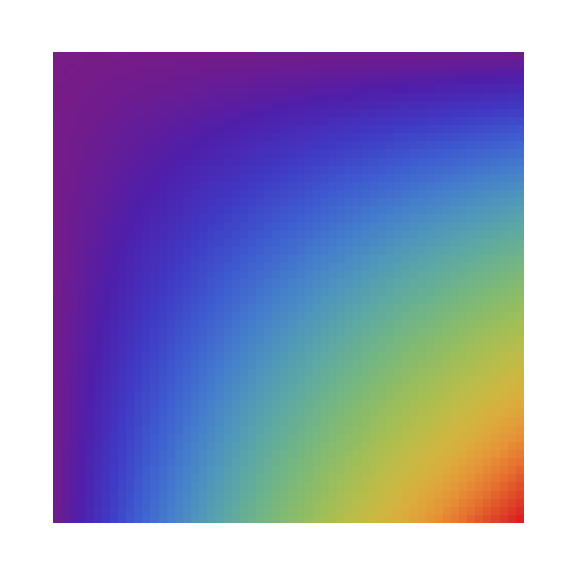

```mathematica
n=17;
ArrayPlot[
Table[i*j,{i,1,Prime[n]-1},{j,1,Prime[n]-1}],
AspectRatio->1,ImageSize->Large,ColorFunction->"Rainbow"]
```

Let’s animate the order

```mathematica
Animate[
ArrayPlot[
Table[MultiplicativeOrder[i*j,n],{i,1,EulerPhi[n],1},{j,1,EulerPhi[n],1}],
AspectRatio->1,ImageSize->Large],
{n,2,100,1}]
```

Now we will look at the table of units mod the nth prime.

```mathematica
n=17;
ArrayPlot[
Table[Mod[i*j,Prime[n]],{i,1,Prime[n]-1},{j,1,Prime[n]-1}],
AspectRatio->1,ImageSize->Large]
```

```mathematica
ColorData[]
ColorData["Gradients"][[16]]
```

```mathematica
n=17;
Table[ArrayPlot[Table[Mod[i*j,Prime[n]],{i,1,Prime[n]-1},{j,1,Prime[n]-1}],ColorFunction->ColorData["Gradients"][[k]],AspectRatio->1,ImageSize->Large],{k,1,Length[ColorData["Gradients"]],1}]
```

```mathematica
ArrayPlot[Table[Mod[2^i*2^j,Prime[n]],{i,1,Prime[n]-1},{j,1,Prime[n]-1}],ColorFunction->"Rainbow"]
```

```mathematica
Length[listofGens]
```

You can use member Q to see if this works.

```mathematica
n=29;
Animate[
listofGens=PrimitiveRootList[Prime[n]];
ArrayPlot[Table[If[MemberQ[listofGens,Mod[i*j,Prime[n]]],Mod[i*j,Prime[n]],0],{i,1,(Prime[n]-1)/2},{j,1,(Prime[n]-1)/2}],ColorRules->{0->Black,_->Yellow}],{n,1,100,1}]
```

## On the table of orders of similar groups

From: https://library.wolfram.com/infocenter/MathSource/696/

This: https://mathematica.stackexchange.com/questions/126376/finding-the-group-of-residue-classes-modulo-n-under-multiplication

is also interesting

```mathematica
invphi[m_Integer]:=Module[
{main,init,genp,bestcand,gencand,addcand,genans,
Lp,Lq,r,s,r0,Mdiv},

main[]:=Module[
{ans={},wrk,threshold=100,
Lstate,Ladd,quo,indx,i},
wrk={{Table[0,{r}],m}};
wrk[[1,1,1]]=-1;
For[i=1,i≤Length[wrk],i++,
If[i==threshold+1,
ans={ans,genans[Take[wrk,threshold] ] };
wrk=Drop[wrk,threshold];
i=1
];
{Lstate,quo}=wrk[[i]];
indx=bestcand[Lstate,quo];
Ladd=gencand[Lstate,indx];
wrk=Join[wrk,addcand[Lstate,quo,Ladd] ]
];
Flatten[{ans,genans[wrk]}]
];

init[]:=Module[
{Lb,Lpq},
{Lq,Lb}=Transpose[FactorInteger[m]];
genp[Lb];
Lpq=Intersection[Lp,Lq];
{Lp,Lq}=Join[Lpq,
Complement[#,Lpq] ]&/@
{Lp,Lq};
{r,s,r0}=Length/@{Lp,Lq,Lpq};
Mdiv=Cases[
Range[r],
x_/;Mod[Lp[[x]]-1,#]==0
]&/@Lq;
];

genp[Lb_]:=Module[
{Lpow,tmp},
Lpow=MapThread[
Table[#1^i,{i,0,#2}]&,
{Lq,Lb}];
Lp={};
Outer[
If[PrimeQ[tmp=Times[##]+1],
Lp={Lp,tmp}
]&,
Sequence@@Lpow];
Lp=Flatten[Lp];
];

bestcand[Lstate_,quo_]:=Module[
{len=Infinity,indx=0,cur,i},
For[i=1,i≤s,i++,
If[((i≤r0&&
Lstate[[i]]≠1)||
i>r0)&&
Mod[quo,Lq[[i]] ]==0,
cur=Length[Mdiv[[i]] ];
If[cur<len,
len=cur;
indx=i
]
]
];
indx
];

gencand[Lstate_,indx_]:=Module[
{Ladd},
Ladd=
If[indx≠0,
If[indx≤r0,
Prepend[Mdiv[[indx]],indx],
Mdiv[[indx]]
],
Range[r]
];
Select[Ladd,Lstate[[#]]==0&]
];

addcand[Lstate_,quo_,Ladd_]:=Module[
{ans={},Lstate2,quo2,len,i},
len=Length[Ladd];
For[i=1,i≤len,i++,
Lstate2=ReplacePart[Lstate,1,Ladd[[i]] ];
quo2=quo/(Lp[[Ladd[[i]] ]]-1);
(Lstate2[[Ladd[[#]] ]]=-1)&/@
Range[i-1];
If[Lstate2[[#]]==0&&
Mod[quo2,Lp[[#]]-1]≠0,
Lstate2[[#]]=-1]&/@
Range[r];
AppendTo[ans,{Lstate2,quo2}]
];
ans
];

genans[L_]:=Module[
{ans={},Lstate,quo,res,add2,i,j},
For[i=1,i≤Length[L],i++,
{Lstate,quo}=L[[i]];
For[add2=0,add2≤1,add2++,
If[add2==1,
Lstate[[1]]=1
];
For[j=1,j≤s,j++,
If[((j≤r0&&
Lstate[[j]]≠1)||
j>r0)&&
Mod[quo,Lq[[j]] ]==0,
Break[]
]
];
If[j≠s+1,
Continue[]
];
res=Cases[
Transpose[{Lp,Lstate}],
{x_,1}->x];
res=m Times@@res/Times@@(res-1);
ans={ans,res}
]
];
ans
];

Switch[m,
0,Return[{0}],
1,Return[{1,2}],
_?(OddQ[#]||Negative[#]&),Return[{}]
];
init[];
main[]
]
```

So that is how we get interesting numbers... 

Here is how we get our hands on the set of units mod[n]

```mathematica
U[n_]:=Select[Table[i,{i,n}],CoprimeQ[#,n]&]
```

{100,88,41,82,75,150,55,110,132}

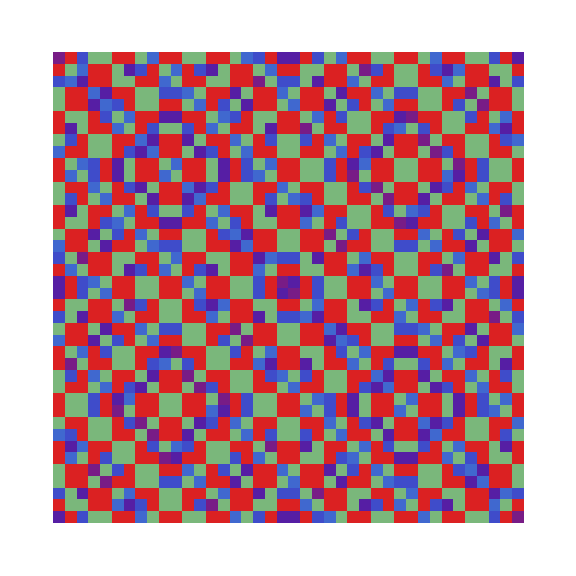
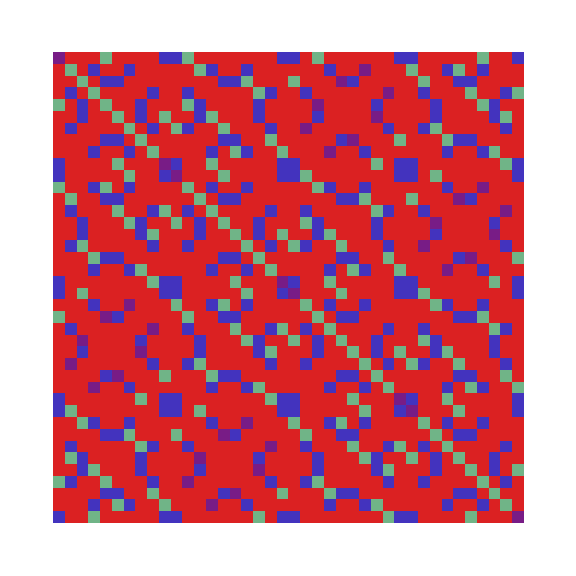
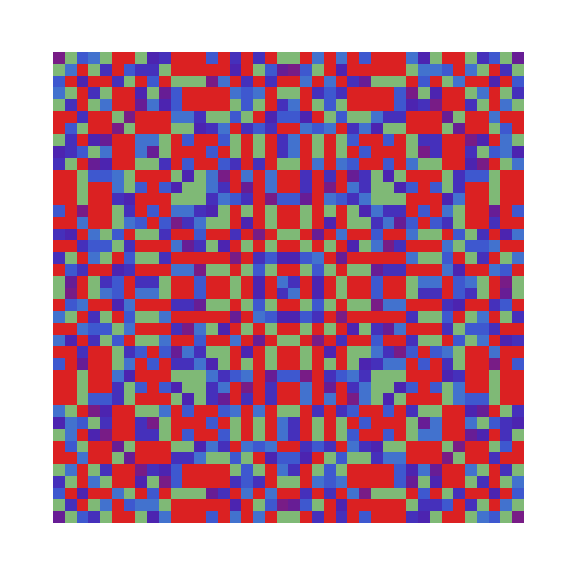
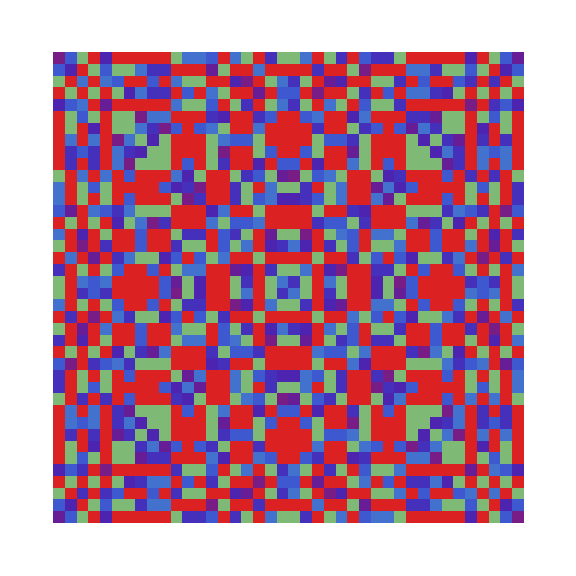
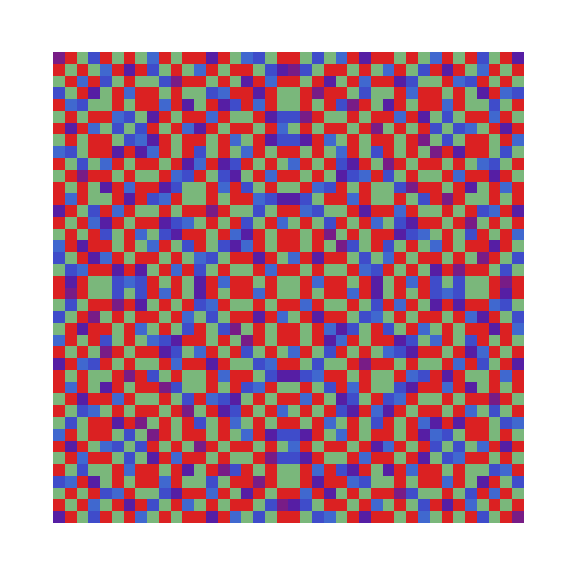
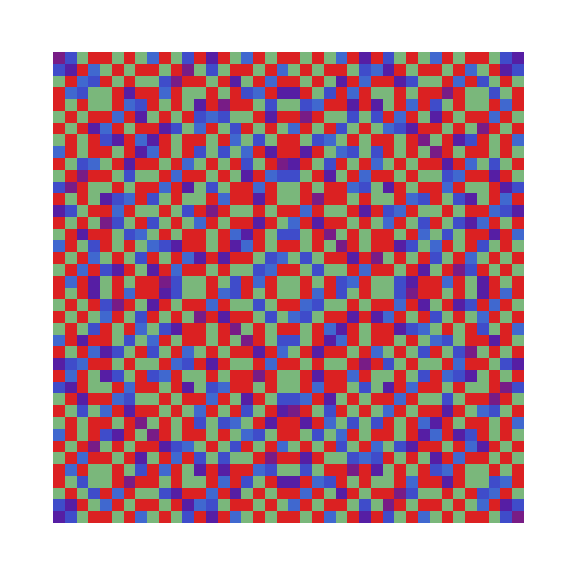
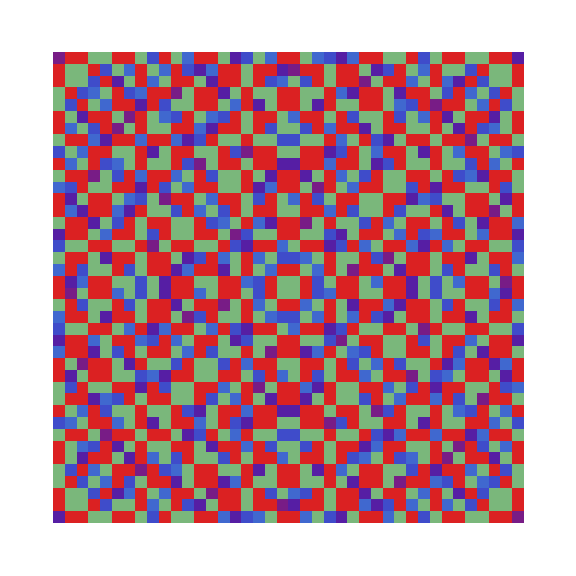
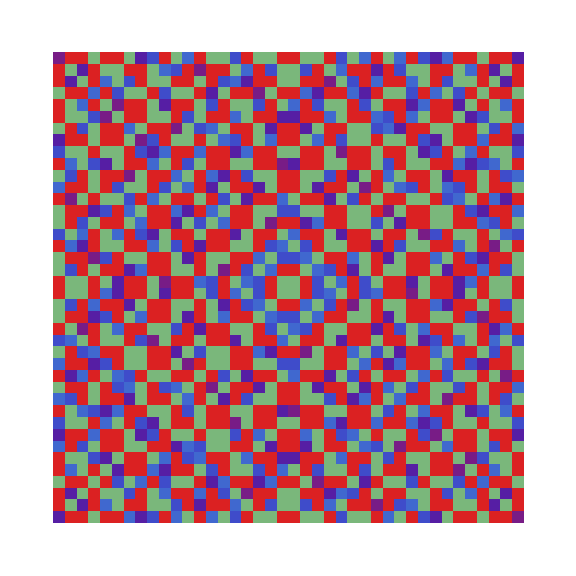

```mathematica
data=invphi[40]
Table[
ArrayPlot[
Table[MultiplicativeOrder[i*j,m],{i,U[m]},{j,U[m]}],
AspectRatio->1,ImageSize->Large,ColorFunction->"Rainbow"],
{m,data}]
```